## Figure 2.12:

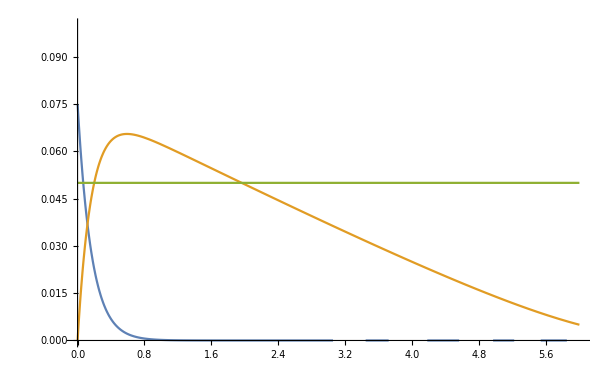
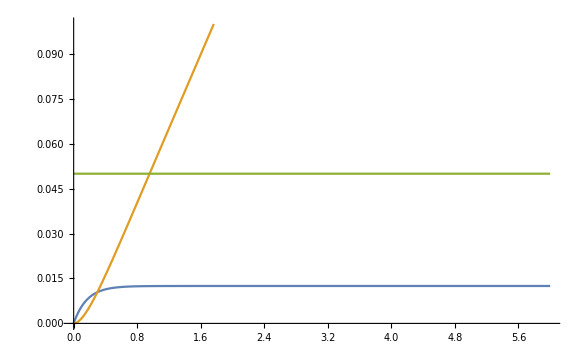

```mathematica
Module[{k1,k2,k3,c1,c2,M,I,cs,c0,soln1,soln2},
M=0.005;
k1=6;
k2=k1;
k3=0.014;
cs=.025;
c0=0;
I=3/1 cs;
soln1=NDSolve[
{c1'[t]==-k1 c1[t],c1[0]==3cs,
c2'[t]==k2 c1[t]-(k3 c2[t])/(c2[t]+M),c2[0]==0},
{c1,c2},{t,0,6}];
soln2=NDSolve[
{c1'[t]==I-k1 c1[t],c1[0]==c0,
c2'[t]==k2 c1[t]-(k3 c2[t])/(c2[t]+M),c2[0]==0},
{c1,c2},{t,0,6}];
{Plot[{c1[t]/.soln1,c2[t]/.soln1,0.05},{t,0,6},PlotRange->{{0,6},{0,.1}}],
Plot[{c1[t]/.soln2,c2[t]/.soln2,0.05},{t,0,6},PlotRange->{{0,6},{0,.1}}]}]
```

## Figure 2.13:

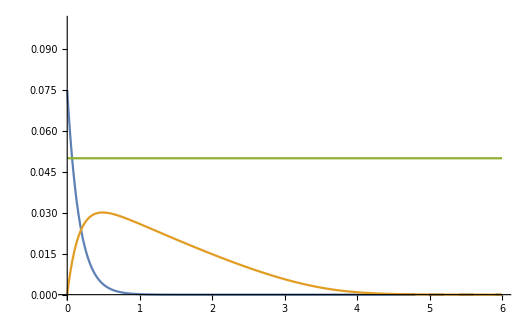
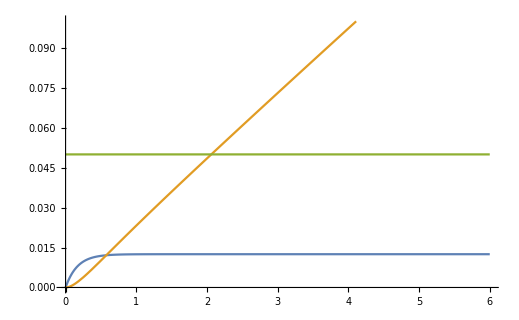

```mathematica
Module[{k1,k2,k3,c1,c2,M,I,cs,c0,soln1,soln2},
M=0.005;
k1=6;
k2=k1/2;
k3=0.014;
cs=.025;
c0=0;
I=3/1 cs;
soln1=NDSolve[
{c1'[t]==-k1 c1[t],c1[0]==3cs,
c2'[t]==k2 c1[t]-(k3 c2[t])/(c2[t]+M),c2[0]==0},
{c1,c2},{t,0,6}];
soln2=NDSolve[
{c1'[t]==I-k1 c1[t],c1[0]==c0,
c2'[t]==k2 c1[t]-(k3 c2[t])/(c2[t]+M),c2[0]==0},
{c1,c2},{t,0,6}];
{Plot[{c1[t]/.soln1,c2[t]/.soln1,0.05},{t,0,6},PlotRange->{{0,6},{0,.1}}],
Plot[{c1[t]/.soln2,c2[t]/.soln2,0.05},{t,0,6},PlotRange->{{0,6},{0,.1}}]}]
```

## Question 2.16

### Without Food

```mathematica
Manipulate[Module[{csm,csw,IM,IW,W,M,n,cs,c0m,c0w,C1,C2,k1,k2,k3m,k3w,sM,sW},
W=55;
csm=14/(.82 W) 1/10;
csw=14/(.67 W) 1/10;
M=.005;
n=a;
c0m=0 csm;
c0w=0csw;
IM=n csm;
IW=n csw;
k1=6;
k2=k1;
k3m=8/(W 0.82 10);
k3w=8/(W 0.67 10);
sM=NDSolve[{C1'[t]==IM-k1 C1[t],C1[0]==c0m,
C2'[t]==k2 C1[t]-(k3m C2[t])/(C2[t]+M),C2[0]==0},{C1,C2},{t,0,25}];
sW=NDSolve[{C1'[t]==IW-k1 C1[t],C1[0]==c0w,
C2'[t]==k2 C1[t]-(k3w C2[t])/(C2[t]+M),C2[0]==0},{C1,C2},{t,0,25}];
Show[Plot[{C1[t]/.sM,C2[t]/.sM,.05,(M k2 IM)/(k1 k3m-k2 IM)},{t,0,25},
PlotRange->{{0,25},{0,.1}},
PlotStyle->{Black,Gray,LightGray},PlotLegends->{"Male GI-Track BAL","Male Blood BAL","Legal Limit","Male Equalibrium"}],

Plot[{C1[t]/.sW,C2[t]/.sW,(M k2 IW)/(k1 k3w-k2 IW)},{t,0,25},
PlotStyle->{Directive[Gray,Dashed],
Directive[Black,Dashed]},
PlotLegends->{"Female GI-Track BAL","Female Blood BAL""Male Equalibrium"}]]

],{{a,.52},0,3,.005}]
```

### With Food

```mathematica
Manipulate[Module[{csm,csw,IM,IW,W,M,n,I,cs,c0m,c0w,C1,C2,k1,k2,k3m,k3w,sM,sW},
W=55;
csm=14/(.82 W) 1/10;
csw=14/(.67 W) 1/10;
M=.005;
n=a;
c0m=0 csm;
c0w=0csw;
IM=n csm;
IW=n csw;
k1=6;
k2=k1/2;
k3m=8/(W 0.82 10);
k3w=8/(W 0.67 10);
sM=NDSolve[{C1'[t]==IM-k1 C1[t],C1[0]==c0m,
C2'[t]==k2 C1[t]-(k3m C2[t])/(C2[t]+M),C2[0]==0},{C1,C2},{t,0,6}];
sW=NDSolve[{C1'[t]==IW-k1 C1[t],C1[0]==c0w,
C2'[t]==k2 C1[t]-(k3w C2[t])/(C2[t]+M),C2[0]==0},{C1,C2},{t,0,6}];
{Show[Plot[{C1[t]/.sM,C2[t]/.sM,.05,(M k2 IM)/(k1 k3m-k2 IM)},{t,0,6},
PlotRange->{{0,6},{0,.1}},
PlotStyle->{Black,Gray,LightGray},
PlotLegends->{"Male GI-Track BAL","Male Blood BAL","Legal Limit","Male Equalibrium"}],

Plot[{C1[t]/.sW,C2[t]/.sW},{t,0,6},
PlotStyle->{Directive[Gray,Dashed],
Directive[Black,Dashed]},
PlotLegends->{"Female GI-Track BAL","Female Blood BAL"}]],(k1 k3m .05)/(k2 (.05+M)),n csm}
],{{a,1.04},0,3,.005}]
```